```mathematica
SeedRandom[1];
arrival=RandomChoice[{-1,1},150]*RandomVariate[BinomialDistribution[20,1/2],150];
```

```mathematica
Expectation[a,a\[Distributed]arrival]
```

-3/2

```mathematica
Probability[a>0,a\[Distributed]arrival]
```

13/30

```mathematica
est=EstimatedDistribution[arrival,MixtureDistribution[{1/2,1/2},{NormalDistribution[a,b],NormalDistribution[c,d]}]]
```

MixtureDistribution[{1/2,1/2},{NormalDistribution[10.1077,2.29463],NormalDistribution[-10.3765,2.43492]}]

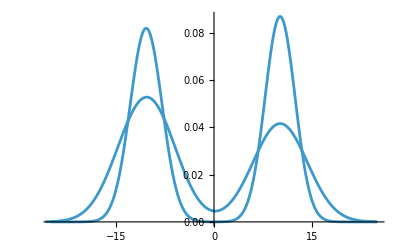

```mathematica
Show[Plot[PDF[est,x],{x,-25,25}],SmoothHistogram[arrival]]
```

```mathematica
DistributionFitTest[arrival,est]
```

0.159936

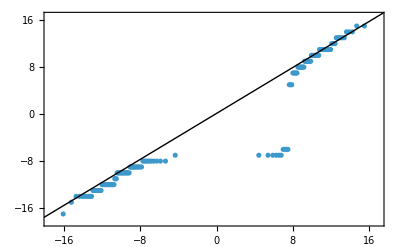

```mathematica
QuantilePlot[arrival,est]
```